### The Solution of u_t + (f(u))_x=0 with the Riemann data u(x,0)=Piecewise[{{uL, x < 0}, {uR, x ≥ 0}}] The exact solution is calculated using the article by Osher which is available here: www.ams.org/proc/1983-089-04/S0002...X/S0002-9939-1983-0718989-X.pdf Also refer “Finite-Volume Methods For Hyperbolic Problems” By LeVeque.

## Biswarup Biswas biswarupb7@gmail.com

### By using this code one can get the analytic solution of known scalar Riemann problems for conservation laws.

```mathematica
xL=-1;xR=1; (* The domain *)
uL=π/4;uR=(15 π)/4; (* Note that uL < uR *)
f[v_]:=Sin[v]; (* Define flux here *)
(*uL=1;uR=0;*) (* Note that uL > uR *)
(*f[v_]:=v^2/(v^2+1/2(1-v)^2); *)(* Define flux here *)
Ngrid=100;(* Define grid number here *)
dx=(xR-xL)/(Ngrid-1); (* Mesh size *)
t=1; (* The time *)
For[i=1,i≤Ngrid,i++,xgrid[i]=xL+(i-1)dx ];
uexact=Table[ ArgMin[{f[v]-xgrid[i]/t v, uL≤v≤uR},v],{i,1,Ngrid}];(* This is the case when uL ≤ uR *)
(*uexact=Table[x=xL+(i-1)dx ; ArgMax[{f[v]-x/t v, uR≤v≤uL},v],{i,1,Ngrid}];*) (* This is the case when uL ≥ uR *)
x=Array[xgrid,Ngrid];
```

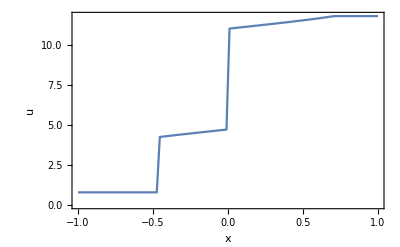

```mathematica
ListLinePlot[Thread[{x,uexact}],AxesLabel->{HoldForm[x],HoldForm[u]},Frame->True]  (* To plot *)
```

```mathematica
(*Export["uexact.mat",Thread[{x,uexact}],"MAT"] ;*)(* To export in MAT file *)
```